```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

```mathematica
Manipulate[
Plot[ 
Abs[E^(-I Pi u) + (e + Sqrt[e^2 + 1]) E^(I Pi u)]^2
, {u, -1/2, 1/2}
, PlotRange -> {Full, {0, 100}}
],
{e, 0, 10}]
```

```mathematica
Clear[rho, t]
rho[u_, e_] = Module[{r, n},
r[uu_, ee_] = Abs[E^(-I Pi uu) + (ee + Sqrt[ee^2 + 1]) E^(I Pi uu)]^2 ;
n[ee_] = Assuming[ ee ≥ 0 && uu ∈Reals, Integrate[ r[uu, ee], {uu, -1/2, 1/2}]] ;
r[u, e]/n[e]
] 

t = Table[ rho[u,e],{e, 0, 10, 2} ] ;
```

(Abs[ⅇ^(-ⅈ π u)+(e+√(1+e^2)) ⅇ^(ⅈ π u)]^2)/(2 (1+e^2+e √(1+e^2)))

```mathematica
(Abs[ⅇ^(-ⅈ π u)+(e+√(1+e^2)) ⅇ^(ⅈ π u)]^2)/(2 (1+e^2+e √(1+e^2)))// TraditionalForm
```

(Abs[ⅇ^(ⅈ π u) (e+√(e^2+1))+ⅇ^(-ⅈ π u)]^2)/(2 (e^2+√(e^2+1) e+1))

1/2 Abs[ⅇ^(-ⅈ π u)+ⅇ^(ⅈ π u)]^2

(Abs[ⅇ^(ⅈ π u) (e+√(e^2+1))+ⅇ^(-ⅈ π u)]^2)/(2 (e^2+√(e^2+1) e+1))

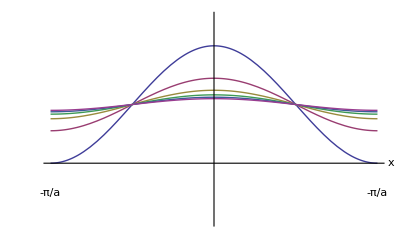

```mathematica
t[[1]] // TraditionalForm
rho[u, e] // TraditionalForm
(*Integrate[t[[1]], {u, -1/2, 1/2}]*)
(*Integrate[t[[3]], {u, -1/2, 1/2}]*)

pp =Plot[ Evaluate@t
, {u, -1/2, 1/2}
,Ticks -> None
, AxesLabel -> {x, None}
, Epilog -> { Text[-Pi/a,{-1/2, -0.5}], Text[-Pi/a,{1/2, -0.5}] }
, PlotRange -> {Full, {-1, 2.5}}
]
```

```mathematica
peeters`exportForLatex["ps7p2eFig1", pp]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/ps7p2eFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/ps7p2eFig1pn.png}